70

1

0

70 (1+te)-70 (1+te)^(3/2)

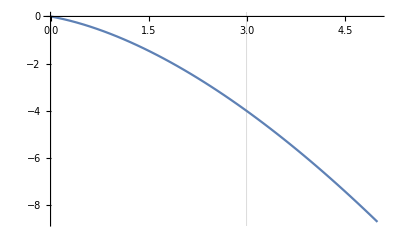

0.3

0.7

70 (1+te)-70 (1+te) √(0.7/(1+te)^2+0.3 (1+te))

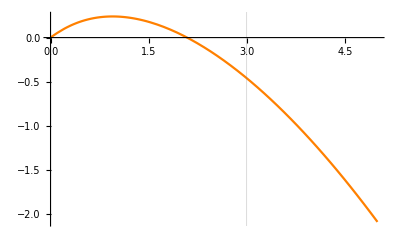

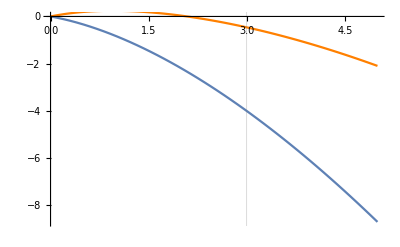

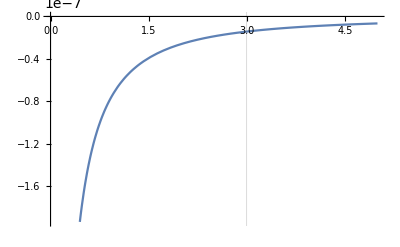

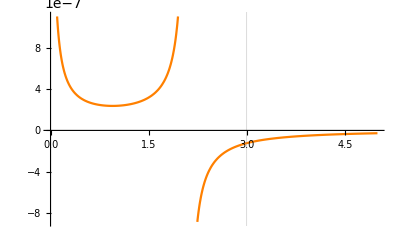

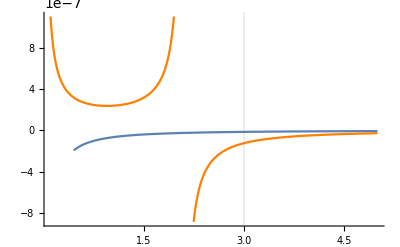

```mathematica
(* Part B *)
Clear[te,a1,a2,a3,a4]
H0=70
Ωm = 1
ΩΛ = 0
zdot1= H0(1+te)-(H0(1+te)Sqrt[Ωm(1+te)+ΩΛ /(1+te)^2])
a1=Plot[zdot1/H0, {te, 0,5},GridLines->{{3},{}}]
Ωm1= 0.3
ΩΛ1= 0.7
zdot2= H0(1+te)-(H0(1+te)Sqrt[Ωm1(1+te)+ΩΛ1/(1+te)^2])
a2=Plot[zdot2/H0, {te, 0,5},GridLines->{{3},{}},PlotStyle->{Orange}]
Show[a1,a2]

(* Part C *)
a3 = Plot[(4*10^(-6))/zdot1, {te, 0,5},GridLines->{{3},{}}]
a4 = Plot[(4*10^(-6))/zdot2, {te, 0,5},GridLines->{{3},{}},PlotStyle->{Orange}]
Show[a3,a4, PlotRange-> All]
```